# Stellar Evolution Simulator Reese Danzer & Karthik Boyareddygari

## Output:

```mathematica
interface[]
```

## Main Code:

```mathematica
interface[]:=
DynamicModule[{
maxStep=Length[oneMSunData],
maxAge=Max[one["Age"]],
maxRadius=Max[one["Radius"]],
maxLuminosity=Max[one["Luminosity"]],
maxTSurface=Max[one["T_s"]],
color,radius,surfaceTemp,centerTemp,luminosity,stepFunction
},
Manipulate[
stepFunction=InverseFunction[Interpolation[Normal[oneMSun[All,"Age"]]]];
color=fancyInterpolate[age,"Radius",stepFunction]^-1;
radius=fancyInterpolate[age,"Radius",stepFunction];
luminosity=fancyInterpolate[age,"Luminosity",stepFunction];
surfaceTemp=fancyInterpolate[age,"T_s",stepFunction];
centerTemp=fancyInterpolate[age,"T_c",stepFunction];
(*This will be the list of changing variables to be used below, because if we just slap the commands in themselves it will get really cluttered really fast.*)
GraphicsGrid[{
{Graphics3D[{Hue[color],Tooltip[Sphere[{0,0,0} ,radius]]},Background->Black,Boxed->False,PlotRange->maxRadius],
(*The Sphere Graphic*)
Panel[Graphics[PlotRange->{{maxTSurface,0},{0,maxLuminosity}},Axes->True,GridLines->Automatic, Background->Black,AxesStyle->Directive[Red],AxesLabel->{"T_s","L⊙"},Epilog->{Darker[Yellow,0.2],PointSize->0.04,Point[{surfaceTemp,luminosity}]}],Background->Black]},
(*The HR Diagram*)
{Graphics[{Hue[0.02],Tooltip[Disk[{0,0},1]],Hue[0.15],Tooltip[Disk[{0,0},1/age]]},PlotRange->1.1,Background->Darker[Gray,0.75]],
(*The Internal Diagram*)
Panel[Graphics[{FontSize->16, Text[
"Surface Temperature: "<>ToString[NumberForm[Round[surfaceTemp],DigitBlock->3]]<>"°K"<>
"\nCenter Tempurature: "<>ToString[NumberForm[Round[centerTemp],DigitBlock->3]]<>"°K"<>"\nRadius: "<>ToString[NumberForm[radius,DigitBlock->3,NumberSeparator->","]]<>" R⊙"<>
"\nLuminosity: "<>ToString[NumberForm[luminosity,DigitBlock->3,NumberSeparator->","]]<>" L⊙"<>
"\nAge: "<>ToString[AccountingForm[age,DigitBlock->3,NumberSeparator->","]]<>" Years"]}]]}
(*The Text Readouts*)
},
ContentSelectable->False,
(*So they don't get their grubby hands on our nice animation.*)
ImageSize->Full
],
{age,1,maxAge},ContentSize->{600,600}]
]
```

## Dataset Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
oneMSunData=Import["One Solar Mass.txt","Table"];
oneMSun=Dataset[Table[
<|"Age"->oneMSunData[[i,2]],"Mass"->oneMSunData[[i,3]],"Luminosity"->10^oneMSunData[[i,4]],"Radius"->10^oneMSunData[[i,5]],"T_s"->10^oneMSunData[[i,6]],"T_c"->10^oneMSunData[[i,7]],"ρ_c"->10^oneMSunData[[i,8]],"P_c"->10^oneMSunData[[i,9]],"R_He"->oneMSunData[[i,27]],"R_C"->oneMSunData[[i,28]],"R_O"->oneMSunData[[i,29]]|>,
{i,Length[oneMSunData]}]
];
```

```mathematica
initialize[data_]:=
Module[{association},
association=<|"Age"->data[[All,2]],"Mass"->data[[All,3]],"Luminosity"->10^data[[All,4]],"Radius"->10^data[[All,5]],"T_s"->10^data[[All,6]],"T_c"->10^data[[All,7]],"ρ_c"->10^data[[All,8]],"P_c"->10^data[[All,9]],"R_He"->data[[All,27]],"R_C"->data[[All,28]],"R_O"->data[[All,29]]|>;
Return[association];
]
```

```mathematica
one=initialize[oneMSunData];
```

## Complex Interpolation

```mathematica
fancyInterpolate[age_,qty_,f_]:=
Module[{step},
step=f[age];
Return[
Interpolation[
connect[{one["Age"][[Round[step]-3;;Round[step]+3]],
one[qty][[Round[step]-3;;Round[step]+3]]}],age]
]
];
```

{0.,50000.,100000.,160000.,232000.}

## Connect

```mathematica
connect[listoflist_]:=(*assume that all lists in listoflist are of the same length because we are inputting them*)
Module[{length=Length[listoflist[[1]]],lengthmain=Length[listoflist],final},
final=Table[listoflist[[k,i]],{i,1,length},{k,1,lengthmain}];(*create a list of length lists each being lengthmain elements long*)
Return[final]
]
```

## Datasets:

```mathematica
Dynamic[one]//Table
```

## Variable Explanations:

Age: A number from 0 to 1 that represents the position the data point represents in the star’s life.
Mass: Mass of the star in M⊙.
Radius: Radius of the star, in R⊙.
Luminosity: Luminosity of the star, in L⊙.

## Data Graphs:

## One Msun:

#### Age

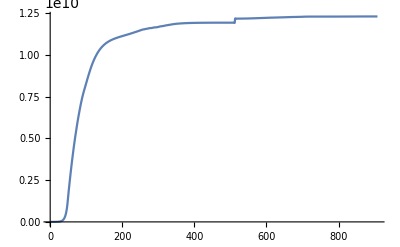

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Age"]]][x],{x,1,908},PlotRange->Full]
```

#### Mass

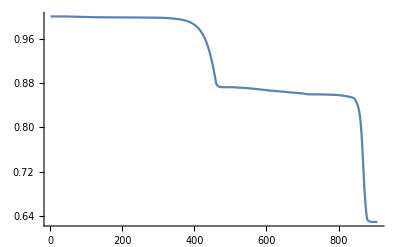

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Mass"]]][x],{x,1,908},PlotRange->Full]
```

#### Radius

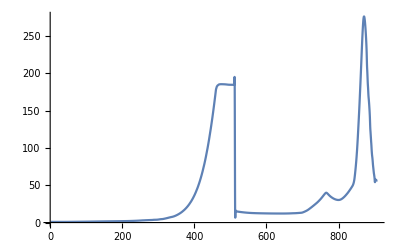

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Radius"]]][x],{x,1,908},PlotRange->Full]
```

#### Luminosity

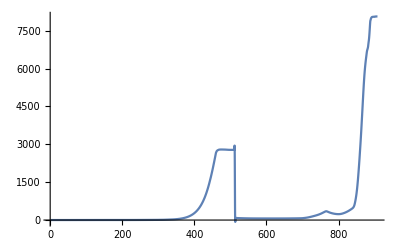

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Luminosity"]]][x],{x,1,908},PlotRange->Full]
```

#### Surface Tempurature

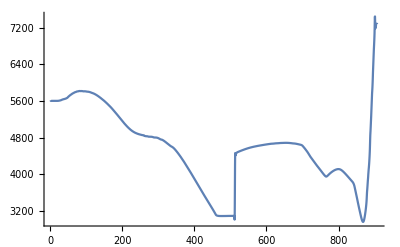

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"T_s"]]][x],{x,1,908},PlotRange->Full]
```

#### Center Tempurature

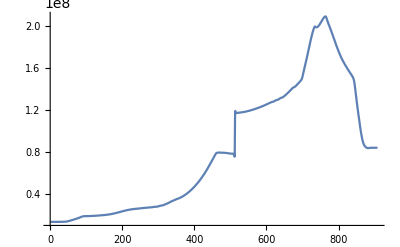

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"T_c"]]][x],{x,1,908},PlotRange->Full]
```